### Calculate coefficient of determination function

```mathematica
CoefficientRR[ y_, f_]:= 1 - (#.#&[y - f ])/(#.#&[y - Mean[y]])(*Формула для вычисления коэффициента детерминации*)
```

## Data import and formatting

```mathematica
SetDirectory[NotebookDirectory[]];
rawData = Import["summary_SDB (1).xlsx"];
rawData =rawData⟦1⟧;
```

```mathematica
rawData//MatrixForm
```

( |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  | Medium with 5% FBS |  |  |  |  |  |  |  |  |  |  |  |  |  |  | Serum-free medium |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  | Luminescence (RLU) |  |  |  |  |  |  | Fluorescence (RFU) |  |  |  |  |  |  |  | Luminescence (RLU) |  |  |  |  |  |  | Fluorescence (RFU) |  |  |  |  |  | 
Tme point | Date | Time (h) | 50 µg/ml | 10 µg/ml | 1 µg/ml | 0.1 µg/ml | 0.01 µg/ml | 0 µg/ml | PC | 50 µg/ml | 10 µg/ml | 1 µg/ml | 0.1 µg/ml | 0.01 µg/ml | 0 µg/ml | PC |  | 50 µg/ml | 10 µg/ml | 1 µg/ml | 0.1 µg/ml | 0.01 µg/ml | 0 µg/ml | PC | 50 µg/ml | 10 µg/ml | 1 µg/ml | 0.1 µg/ml | 0.01 µg/ml | 0 µg/ml | PC
T0 | 20.07.2022 21:35:59 | 0. | 1.17887×10^6 | 1.1992×10^6 | 1.46962×10^6 | 1.44045×10^6 | 1.40745×10^6 | 1.21322×10^6 | 4299. | 30.3983 | 44.9908 | 30.2558 | 32.5633 | 31.4208 | 28.5118 | 0.807667 |  | 908694. | 1.17092×10^6 | 1.16969×10^6 | 1.09737×10^6 | 1.08577×10^6 | 881344. | 4797.33 | 7.44808 | 8.83483 | 11.2198 | 12.4548 | 15.4123 | 24.5023 | 57.594
T1 | 21.07.2022 00:34:55 | 3. | 2.3114×10^6 | 2.3044×10^6 | 3.05715×10^6 | 2.9089×10^6 | 2.8469×10^6 | 2.4469×10^6 | 2670.33 | 37.014 | 53.0465 | 39.599 | 47.154 | 42.819 | 35.8743 | 1.08567 |  | 771995. | 2.41034×10^6 | 2.28359×10^6 | 2.19109×10^6 | 2.10184×10^6 | 1.58434×10^6 | 853.667 | 16.7827 | 13.0865 | 14.405 | 24.3165 | 28.464 | 41.7465 | 70.639
T2 | 21.07.2022 09:57:58 | 12.5 | 2.93206×10^6 | 2.68181×10^6 | 3.79406×10^6 | 3.73956×10^6 | 3.84281×10^6 | 3.42456×10^6 | 0. | 45.9522 | 66.1472 | 45.8047 | 50.9122 | 30.0397 | 23.7779 | 3.007 |  | 232397. | 1.67332×10^6 | 1.0539×10^6 | 967897. | 957522. | 806047. | 55.4 | 43.2007 | 22.3737 | 19.7857 | 27.2857 | 24.1882 | 24.9257 | 85.2007
T3 | 21.07.2022 12:56:33 | 15.5 | 2.84842×10^6 | 2.67469×10^6 | 3.60092×10^6 | 3.70417×10^6 | 3.93842×10^6 | 3.44377×10^6 | 0. | 44.0888 | 65.2188 | 45.6438 | 53.2038 | 38.6013 | 29.4951 | 2.34333 |  | 120550. | 1.3036×10^6 | 860030. | 776655. | 842805. | 717230. | 0. | 43.7907 | 22.8857 | 21.3032 | 28.6182 | 29.1707 | 32.6557 | 87.0807
T4 | 21.07.2022 15:53:44 | 18.5 | 3.18434×10^6 | 2.98322×10^6 | 3.89959×10^6 | 4.17634×10^6 | 4.53809×10^6 | 4.05559×10^6 | 0. | 40.2593 | 62.2343 | 45.4143 | 54.2593 | 47.8193 | 38.2121 | 1.075 |  | 81039.2 | 1.05462×10^6 | 871967. | 806692. | 893517. | 733967. | 0. | 41.801 | 27.031 | 22.0335 | 33.491 | 36.166 | 47.4935 | 81.6393
T5 | 21.07.2022 18:55:34 | 21.5 | 2.9683×10^6 | 2.81913×10^6 | 3.6533×10^6 | 3.8593×10^6 | 4.4423×10^6 | 3.92903×10^6 | 0. | 39.767 | 60.592 | 44.5145 | 52.6395 | 49.662 | 37.6188 | 1.008 |  | 46720.4 | 745948. | 757093. | 711943. | 767793. | 668768. | 0. | 41.4375 | 29.7085 | 20.8975 | 32.7125 | 37.4775 | 50.55 | 81.2833
T6 | 21.07.2022 21:54:22 | 24.5 | 3.25796×10^6 | 3.10929×10^6 | 3.90996×10^6 | 4.18646×10^6 | 4.90546×10^6 | 4.10746×10^6 | 0. | 39.4223 | 59.7398 | 45.2298 | 54.3573 | 49.5548 | 37.9301 | 1.04767 |  | 39220. | 668983. | 765910. | 748510. | 788060. | 680760. | 0. | 42.2303 | 32.1883 | 23.1953 | 34.6928 | 38.8103 | 48.2403 | 78.2287
T7 | 22.07.2022 00:44:51 | 27.5 | 3.24315×10^6 | 3.10823×10^6 | 3.86515×10^6 | 4.1689×10^6 | 4.9534×10^6 | 4.28653×10^6 | 0. | 39.276 | 59.3485 | 46.071 | 55.606 | 49.7385 | 37.6653 | 0.978 |  | 28122.6 | 531915. | 640313. | 710613. | 718413. | 625738. | 0. | 43.2462 | 35.1487 | 27.3087 | 36.2762 | 39.6337 | 47.8487 | 82.6203
T8 | 22.07.2022 17:11:06 | 44. | 2.98127×10^6 | 2.95581×10^6 | 3.04519×10^6 | 3.89672×10^6 | 4.82422×10^6 | 4.14497×10^6 | 0. | 35.7735 | 54.966 | 49.8835 | 57.526 | 47.126 | 36.7523 | 0.940667 |  | 7739.7 | 145377. | 210494. | 366297. | 397847. | 345172. | 0. | 41.488 | 49.238 | 42.2605 | 44.263 | 39.388 | 48.6355 | 67.1447
T9 | 22.07.2022 20:08:28 | 47. | 3.20472×10^6 | 3.02563×10^6 | 3.14014×10^6 | 3.99563×10^6 | 4.86963×10^6 | 4.51938×10^6 | 0. | 33.1602 | 54.4252 | 46.8077 | 55.5402 | 45.6952 | 35.8172 | 0.828333 |  | 5951.58 | 89010.8 | 129641. | 261801. | 322789. | 276714. | 0. | 40.9165 | 51.259 | 43.139 | 46.229 | 39.9965 | 48.564 | 67.2907
T10 | 22.07.2022 22:58:02 | 50. | 2.76678×10^6 | 2.72165×10^6 | 2.83391×10^6 | 3.50461×10^6 | 4.29301×10^6 | 4.10276×10^6 | 0. | 32.9665 | 53.774 | 45.8065 | 55.9265 | 45.3765 | 36.336 | 0.908667 |  | 5694.29 | 52343.9 | 79806.4 | 202143. | 283198. | 240773. | 0. | 40.6153 | 54.2678 | 45.3353 | 48.4903 | 40.6728 | 47.6853 | 67.262
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.284138 | 0.29669 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.574736 | 0.617182 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.775792 | 0.76595 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.795093 | 0.726958 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.916157 | 0.787256 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.896819 | 0.737534 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.990322 | 0.789349 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1. | 0.780302 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.97392 | 0.614767 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.983087 | 0.633935 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.866678 | 0.572114 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | )

```mathematica
data = rawData⟦4;;15⟧;
```

```mathematica
ToExpression@First@StringCases[dataᵀ⟦4,1⟧,NumberString]
```

50

```mathematica
dataᵀ⟦3⟧
```

{Time (h),0.,3.,12.5,15.5,18.5,21.5,24.5,27.5,44.,47.,50.}

```mathematica
Rest@dataᵀ⟦4⟧/231000
```

{5.10335,10.0061,12.6929,12.3308,13.785,12.8498,14.1037,14.0396,12.9059,13.8732,11.9774}

```mathematica
Rest@dataᵀ⟦3⟧
```

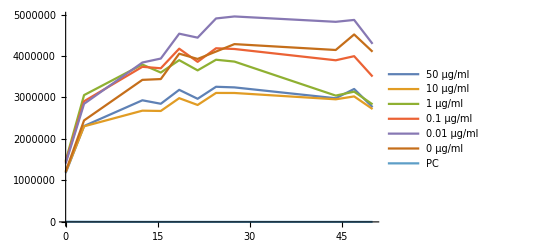

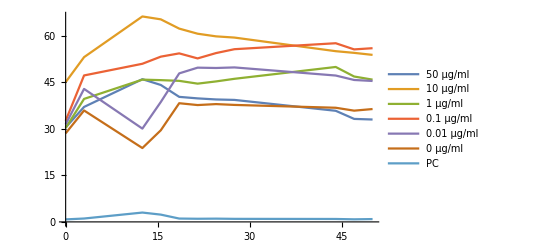

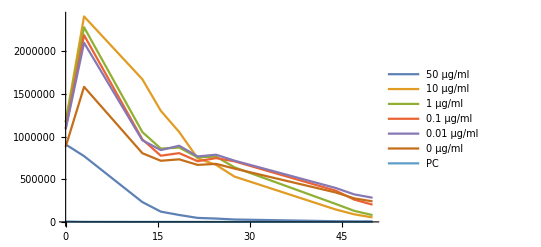

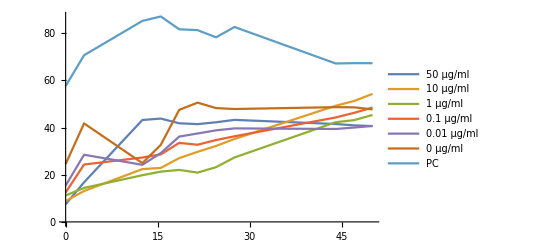

```mathematica
Table[Table[{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦i⟧}ᵀ,{i,j,j+6}],{j,{4,11,19,26}}];
Print@ListLinePlot[#,PlotLegends->data⟦1,4;;10⟧]&/@% ;
```

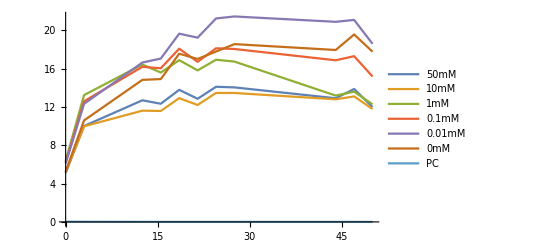

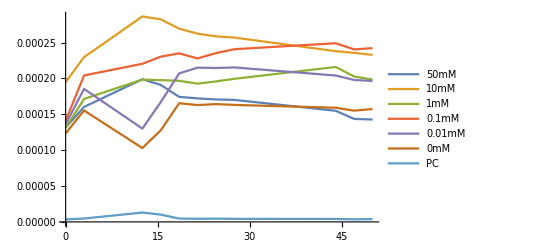

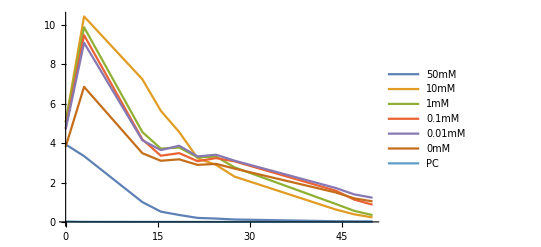

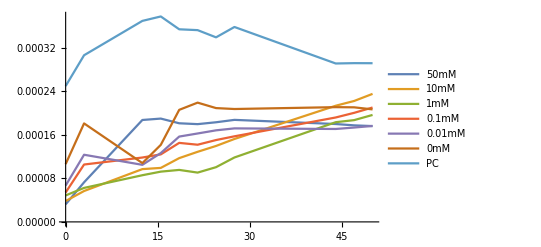

```mathematica
Table[Table[{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦i⟧/231000}ᵀ,{i,j,j+6}],{j,{4,11,19,26}}];
If[StringContainsQ[#, NumberString],StringForm["``mM",First@StringCases[#, NumberString]], "PC"]&/@ data⟦1,4;;10⟧;
Print@ListLinePlot[#,PlotLegends->%]&/@%% ;
```

```mathematica
train0 = Table[Table[{Rest@dataᵀ⟦3⟧,ConstantArray[ToExpression@First@StringCases[dataᵀ⟦i,1⟧,NumberString] ,11],Rest@dataᵀ⟦i⟧/231000}ᵀ,{i,j,j+5}],{j,{4,11,19,26}}];
```

```mathematica
Print@ListPointPlot3D[#]&/@ train0;
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Dimensions[train0]
```

{4,6,11,3}

```mathematica
max = Max[train0⟦All,All, All, 3⟧]
```

21.4433

```mathematica
train1 = ArrayReshape[#/{1,1,max}&/@Flatten[train0,2], {4,66, 3}];
```

```mathematica
firsts = train0⟦All,All,1, 3⟧
```

{{5.10335,5.19134,6.36201,6.23571,6.09285,5.25205},{0.000131595,0.000194766,0.000130978,0.000140967,0.000136021,0.000123428},{3.93374,5.06891,5.06361,4.75052,4.7003,3.81534},{0.0000322428,0.000038246,0.0000485707,0.000053917,0.0000667201,0.000106071}}

```mathematica
train1//Dimensions
```

{4,66,3}

```mathematica
train2 = ArrayReshape[Table[#/{1, 1, firsts⟦i,j⟧}&/@train0⟦i, j⟧,{i,1, 4},{j, 1, 6}], {4, 66,3}];
```

## δ calculations

```mathematica
train0⟦2, -1,All,{1,3}⟧
```

{{0.,0.000123428},{3.,0.0001553},{12.5,0.000102935},{15.5,0.000127684},{18.5,0.00016542},{21.5,0.000162852},{24.5,0.000164199},{27.5,0.000163053},{44.,0.000159101},{47.,0.000155053},{50.,0.000157299}}

```mathematica
train2⟦1, -9;;⟧
```

{{12.5,0,2.82269},{15.5,0,2.83852},{18.5,0,3.34282},{21.5,0,3.2385},{24.5,0,3.38558},{27.5,0,3.53317},{44.,0,3.41649},{47.,0,3.7251},{50.,0,3.3817}}

```mathematica
train2⟦1, -9;;⟧;
#/{1, 1,train0⟦1,-1,3, 3⟧/firsts⟦1,-1⟧}&/@%;
train3 = %
```

{{12.5,0,1.},{15.5,0,1.00561},{18.5,0,1.18427},{21.5,0,1.14731},{24.5,0,1.19941},{27.5,0,1.2517},{44.,0,1.21037},{47.,0,1.3197},{50.,0,1.19804}}

{δ→-0.0071626}

-0.0071626

ⅇ^(0.0071626 (-12.5+t))

Error:0.270404

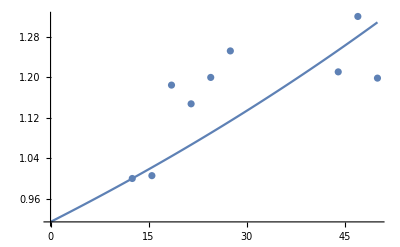

```mathematica
FindFit[train3⟦ All,{1, 3}⟧,ⅇ^(-δ (t-12.5)),{δ}, t]
γ1 = δ/.%
ⅇ^(-δ (t-12.5))/.%%
%/.t-> train3⟦ All,1⟧;
StringForm["Error:``",√((%- train3⟦All, 3⟧)^2//Total)]
Show[Plot[%%%, {t, 0, 50}], ListPlot[train3⟦All, {1,3}⟧], PlotRange-> All]
```

```mathematica
train2⟦3, -10;;⟧
```

{{3.,0,1.79765},{12.5,0,0.914565},{15.5,0,0.813791},{18.5,0,0.832781},{21.5,0,0.758805},{24.5,0,0.772411},{27.5,0,0.709981},{44.,0,0.391642},{47.,0,0.313968},{50.,0,0.273188}}

{δ→0.0459387}

0.0459387

ⅇ^(-0.0459387 (-3+t))

Error:0.218154

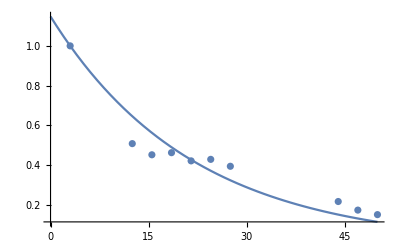

```mathematica
train2⟦3, -10;;⟧;
#/{1, 1,train0⟦3,-1,2, 3⟧/firsts⟦3, -1⟧}&/@%;
train31 = %;
FindFit[train31⟦ All,{1, 3}⟧,ⅇ^(-δ( t-3)),{δ}, t]
γ3 = δ/.%
ⅇ^(-δ (t-3))/.%%
%/.t-> train31⟦ All,1⟧;
StringForm["Error:``",√((%- train31⟦All, 3⟧)^2//Total)]
Show[Plot[%%%, {t, 0, 50}], ListPlot[train31⟦All, {1,3}⟧], PlotRange-> All]
```

## Calculations with exponential models (экспоненциальные модели из курсовой работы)

### Model 1

#### 1.

```mathematica
train0⟦1⟧;
x1 = DeleteCases[%,a_/;a⟦1⟧<10,2];
%⟦;;,1,3⟧;
MapThread[#1⟦;;,3⟧/#2&,{%%,%}];
x1⟦;;,;;, 3⟧= %;
X = Flatten[x1,1]
```

{{12.5,50,1.},{15.5,50,0.971473},{18.5,50,1.08604},{21.5,50,1.01236},{24.5,50,1.11115},{27.5,50,1.1061},{44.,50,1.01678},{47.,50,1.09299},{50.,50,0.94363},{12.5,10,1.},{15.5,10,0.997346},{18.5,10,1.11239},{21.5,10,1.0512},{24.5,10,1.1594},{27.5,10,1.159},{44.,10,1.10217},{47.,10,1.12821},{50.,10,1.01486},{12.5,1,1.},{15.5,1,0.949093},{18.5,1,1.02782},{21.5,1,0.962901},{24.5,1,1.03055},{27.5,1,1.01874},{44.,1,0.80262},{47.,1,0.827645},{50.,1,0.746933},{12.5,0.1,1.},{15.5,0.1,0.990536},{18.5,0.1,1.1168},{21.5,0.1,1.03202},{24.5,0.1,1.11951},{27.5,0.1,1.11481},{44.,0.1,1.04203},{47.,0.1,1.06848},{50.,0.1,0.937171},{12.5,0.01,1.},{15.5,0.01,1.02488},{18.5,0.01,1.18093},{21.5,0.01,1.156},{24.5,0.01,1.27653},{27.5,0.01,1.28901},{44.,0.01,1.25539},{47.,0.01,1.2672},{50.,0.01,1.11715},{12.5,0,1.},{15.5,0,1.00561},{18.5,0,1.18427},{21.5,0,1.14731},{24.5,0,1.19941},{27.5,0,1.2517},{44.,0,1.21037},{47.,0,1.3197},{50.,0,1.19804}}

```mathematica
X1 = #/{1,231.,1}&/@X⟦;;-10⟧;
```

```mathematica
Rest@dataᵀ⟦3,3;;⟧
```

{12.5,15.5,18.5,21.5,24.5,27.5,44.,47.,50.}

```mathematica
ClearAll[t,x]
```

```mathematica
k = 1;
FindFit[X1,{ Exp[-γ1 (x-12.5) + (t μ)/β^2(1-ⅇ^(-β (x-12.5))-β (x-12.5))], μ>0, β>0},{μ ,β},{x,t}, Method->NMinimize]
 Exp[-γ1 (x-12.5) + (t μ)/β^2(1-ⅇ^(-β (x-12.5))-β (x-12.5))]/. %
Show[ ListPointPlot3D[X1],Plot3D[%,{x,0,50},{t, 0,50/231}, AxesLabel->Automatic], PlotRange-> All]
StringForm["μ/β = ``",( μ/β)/. %%%]
(%%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01}/231},{x, Rest@dataᵀ⟦3,3;;⟧}],1];
StringForm["MAE: ``",Mean@Abs[X1⟦;;,3⟧-%]]
StringForm["R:``",CoefficientRR[X1⟦;;,3⟧ , %%]]
```

NMinimize::nnum: The function value «1»[{0,0}] is not a number at {β,μ} = {0.,0.}.

{μ→0.,β→24.105}

ⅇ^(0.+0.0071626 x)

-Graphics3D-

μ/β = 0.

MAE: 0.191586

R:-4.03094

#### 2

```mathematica
FindFit[train⟦k⟧,{ Exp[-0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)], μ>0},{μ ,β},{x,t}]
Exp[- 0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
StringForm["μ/β = ``",( μ/β)/. %%%]
(%%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{μ→6.96741×10^-7,β→25389.3}

ⅇ^(1.08086×10^-15 t (1-ⅇ^(-25389.3 x)-25389.3 x)-0.053 x)

-Graphics3D-

μ/β = 2.74423×10^-11

General::munfl: Exp[-76167.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-317366.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-393534.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 0.974067

R:-22.9575

#### 3.

```mathematica
train0⟦3⟧;
y = DeleteCases[%,a_/;a⟦1⟧<3,2];
%⟦;;,1,3⟧;
MapThread[#1⟦;;,3⟧/#2&,{%%,%}];
y⟦;;,;;, 3⟧= %;
Y = Flatten[y,1]
```

{{3.,50,1.},{12.5,50,0.301034},{15.5,50,0.156154},{18.5,50,0.104974},{21.5,50,0.0605191},{24.5,50,0.0508035},{27.5,50,0.0364284},{44.,50,0.0100256},{47.,50,0.00770936},{50.,50,0.00737608},{3.,10,1.},{12.5,10,0.694225},{15.5,10,0.540837},{18.5,10,0.437538},{21.5,10,0.309478},{24.5,10,0.277546},{27.5,10,0.22068},{44.,10,0.060314},{47.,10,0.0369287},{50.,10,0.0217164},{3.,1,1.},{12.5,1,0.461508},{15.5,1,0.376612},{18.5,1,0.38184},{21.5,1,0.331536},{24.5,1,0.335397},{27.5,1,0.280397},{44.,1,0.0921768},{47.,1,0.0567706},{50.,1,0.0349477},{3.,0.1,1.},{12.5,0.1,0.441741},{15.5,0.1,0.35446},{18.5,0.1,0.368168},{21.5,0.1,0.324926},{24.5,0.1,0.341615},{27.5,0.1,0.324319},{44.,0.1,0.167175},{47.,0.1,0.119484},{50.,0.1,0.0922565},{3.,0.01,1.},{12.5,0.01,0.455563},{15.5,0.01,0.400983},{18.5,0.01,0.425111},{21.5,0.01,0.365295},{24.5,0.01,0.374937},{27.5,0.01,0.341801},{44.,0.01,0.189285},{47.,0.01,0.153574},{50.,0.01,0.134738},{3.,0,1.},{12.5,0,0.508757},{15.5,0,0.452698},{18.5,0,0.463262},{21.5,0,0.42211},{24.5,0,0.429679},{27.5,0,0.39495},{44.,0,0.217864},{47.,0,0.174655},{50.,0,0.15197}}

```mathematica
Y⟦;;-11⟧;
Y1 = #/{1,231.,1}&/@%;
```

```mathematica
k = 3;
FindFit[Y1,{  Exp[-γ3 (x-3) + (t μ)/β^2(1-ⅇ^(-β (x-3))-β (x-3))], μ>0, β>0},{μ ,β},{x,t}, Method->NMinimize]
Exp[-γ3 (x-3) + (t μ)/β^2(1-ⅇ^(-β (x-3))-β (x-3))]/. %
Show[ ListPointPlot3D[Y1],Plot3D[%,{x,0,50},{t, 0,50/231}, AxesLabel->Automatic]]
StringForm["μ/β = ``",( μ/β)/. %%%]
(%%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01}/231},{x, Rest@dataᵀ⟦3,2;;⟧}],1];
StringForm["MAE: ``",Mean@Abs[Y1⟦;;,3⟧-%]]
StringForm["R:``",CoefficientRR[Y1⟦;;,3⟧ , %%]]
```

{μ→0.112331,β→0.182092}

ⅇ^(3.38779 t (1-ⅇ^(-0.182092 (-3+x))-0.182092 (-3+x))-0.0459387 (-3+x))

-Graphics3D-

μ/β = 0.616891

MAE: 0.0514482

R:0.91972

#### 4.

```mathematica
k = 4;
FindFit[train⟦k⟧,{ Exp[-0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)], μ>0},{μ ,β},{x,t}]
Exp[- 0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
StringForm["μ/β = ``",( μ/β)/. %%%]
(%%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{μ→2.13337×10^-7,β→39265.2}

ⅇ^(1.38373×10^-16 t (1-ⅇ^(-39265.2 x)-39265.2 x)-0.053 x)

-Graphics3D-

μ/β = 5.43323×10^-12

General::munfl: Exp[-117796.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-490815.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-608610.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 2.51674

R:-2.97476

### Model 2

```mathematica
k = 1;
FindFit[train⟦k⟧,{Exp[-(δ*t+0.053) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)],μ>0, β>0 , δ>0},{μ,β,δ},{x,t}]
Exp[-(δ*t+0.053) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
(%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{μ→0.0000164006,β→145323.,δ→0.}

ⅇ^(7.76587×10^-16 (1-ⅇ^(-145323. t)-145323. t) t-0.053 x)

-Graphics3D-

General::munfl: Exp[-7.26616×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 2.15206

R:-11.6026

```mathematica
k = 3;
FindFit[train⟦k⟧,{Exp[-(δ*t+0.053) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)],μ>0, β>0 , δ>0},{μ,β,δ},{x,t}]
Exp[-(δ*t+0.053) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
(%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{μ→9.73901,β→199707.,δ→0.000192393}

ⅇ^(2.4419×10^-10 (1-ⅇ^(-199707. t)-199707. t) t+(-0.053-0.000192393 t) x)

General::munfl: Exp[-713.953] is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

General::munfl: Exp[-9.98536×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 0.321901

R:0.263777

### Model 3

```mathematica
k = 3;
FindFit[train⟦k⟧,{Exp[-(δ* t+0.053) x], δ>0},{δ},{x,t}]
Exp[-(δ* t+0.053) x]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
(%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{δ→0.000331456}

ⅇ^((-0.053-0.000331456 t) x)

-Graphics3D-

MAE: 0.319214

R:0.2627

## Calculation with linear models (линейные модели)

{{0.,1.17887×10^6},{3.,2.3114×10^6},{12.5,2.93206×10^6},{15.5,2.84842×10^6},{18.5,3.18434×10^6},{21.5,2.9683×10^6},{24.5,3.25796×10^6},{27.5,3.24315×10^6},{44.,2.98127×10^6},{47.,3.20472×10^6},{50.,2.76678×10^6}}

FittedModel[2.31832×10^6+20362.7 x]

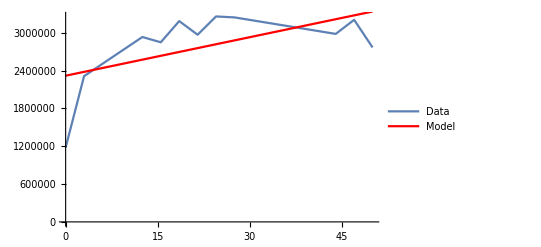

MAE: 378326.

R:0.325236

```mathematica
{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦4⟧}ᵀ
LinearModelFit[%,x,x]
Show[ListLinePlot[%%,PlotLegends->{"Data"}],Plot[%[x],{x,0,50},PlotStyle->Red,PlotLegends->{"Model"}]]
Table[%%[x],{x,Rest@dataᵀ⟦3⟧}];
StringForm["MAE: ``",Mean@Abs[Rest@dataᵀ⟦4⟧-%]]
StringForm["R:``",CoefficientRR[ Rest@dataᵀ⟦4⟧, %%]]
```

{{0.,1.17092×10^6},{3.,2.41034×10^6},{12.5,1.67332×10^6},{15.5,1.3036×10^6},{18.5,1.05462×10^6},{21.5,745948.},{24.5,668983.},{27.5,531915.},{44.,145377.},{47.,89010.8},{50.,52343.9}}

FittedModel[1.79817×10^6-37627. x]

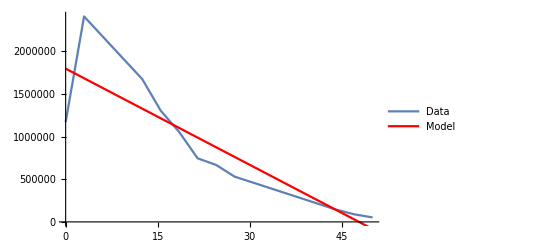

MAE: 246692.

R:0.768515

```mathematica
{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦20⟧}ᵀ
LinearModelFit[%,x,x]
Show[ListLinePlot[%%,PlotLegends->{"Data"}],Plot[%[x],{x,0,50},PlotStyle->Red,PlotLegends->{"Model"}]]
Table[%%[x],{x,Rest@dataᵀ⟦3⟧}];
StringForm["MAE: ``",Mean@Abs[Rest@dataᵀ⟦20⟧-%]]
StringForm["R:``",CoefficientRR[ Rest@dataᵀ⟦20⟧, %%]]
```

### Calculating dynamics of data

```mathematica
slope[lin_]:= ArcTan[D[Normal[lin],x]]
```

Data dynamics: 1.52245×10^6

FittedModel[2.2078×10^6+20065.3 x]

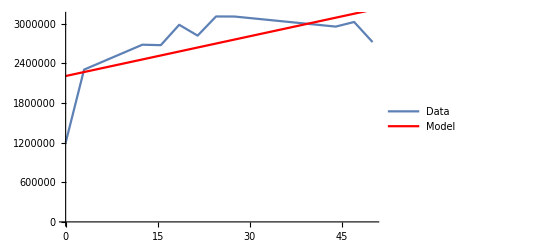

Angle of inclination: 1.57075

```mathematica
StringForm["Data dynamics: ``",(Last@# - First@#)& @Rest@dataᵀ⟦5⟧](*разность между первым измерением и последним*)
{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦5⟧}ᵀ;
LinearModelFit[%,x,x]
Show[ListLinePlot[%%,PlotLegends->{"Data"}],Plot[%[x],{x,0,50},PlotStyle->Red,PlotLegends->{"Model"}]]
StringForm["Angle of inclination: ``",slope[%%]](*угол наклона*)
```

Data dynamics: 2.88953×10^6

FittedModel[2.52766×10^6+44962. x]

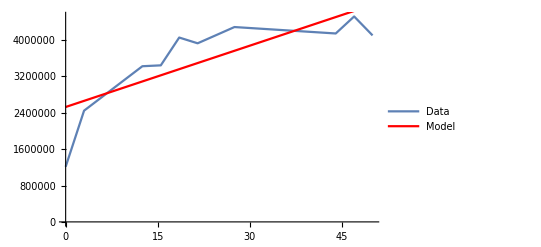

Angle of inclination: 1.57077

```mathematica
StringForm["Data dynamics: ``",(Last@# - First@#)& @Rest@dataᵀ⟦9⟧] (*разность между первым измерением и последним*)
{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦9⟧}ᵀ;
LinearModelFit[%,x,x]
Show[ListLinePlot[%%,PlotLegends->{"Data"}],Plot[%[x],{x,0,50},PlotStyle->Red,PlotLegends->{"Model"}]]
StringForm["Angle of inclination: ``",slope[%%]](*угол наклона*)
```